```mathematica
Draw the Particles For MRI
```

```mathematica
minimumVisibleSphereRad=15/2*10^-6; (*according to Martel et al in 1.5T MRI  
MRI visualization of a single 15 µm navigable imaging agent and future microrobot

 http://ieeexplore.ieee.org/xpl/login.jsp?tp=&arnumber=5626222&url=http%3A%2F%2Fieeexplore.ieee.org%2Fxpls%2Fabs_all.jsp%3Farnumber%3D5626222

http://ieeexplore.ieee.org/xpls/abs_all.jsp?arnumber=5626222&tag=1
*)
VolumeOfSphere[r_]:=4/3 π r^3
MaxLayerThickness = 0.2*10^-6;  (* conversation with Paul R., real range is 50 nm to 250 nm*)
StartingLength = 0.002; (*mm*)
```

```mathematica
N[VolumeOfSphere[minimumVisibleSphereRad]]
```

3.05363×10^-15

```mathematica
VolumeOfSphere[minimumVisibleSphereRad]/(MaxLayerThickness *StartingLength)
```

7.63407×10^-6

```mathematica
Manipulate[

Graphics[{
Gray,Disk[{0,0},minimumVisibleSphereRad],
 rectstart={minimumVisibleSphereRad*2,-minimumVisibleSphereRad};Rectangle[rectstart,rectstart+{VolumeOfSphere[minimumVisibleSphereRad]/(MaxLayerThickness *StartingLength),StartingLength}]
}],
{StartingLength,0.2*10^-4,0.002}]
```

```mathematica
minEdgeLength1p5T = Sqrt[VolumeOfSphere[minimumVisibleSphereRad]/MaxLayerThickness];
StringForm["Min edge length 1.5 T = ``m",NumberForm[minEdgeLength1p5T,3]]
minArea1p5T=VolumeOfSphere[minimumVisibleSphereRad]/MaxLayerThickness;
StringForm["Min area 1.5 T = (``m)^2",NumberForm[minArea1p5T,3]]
```

Min edge length 1.5 T = "0.000094"m

Min area 1.5 T = ^2

```mathematica
minEdgeLength7T = Sqrt[(VolumeOfSphere[minimumVisibleSphereRad](0.2/0.5)^3)/MaxLayerThickness];
StringForm["Min edge length 7T = ``m",NumberForm[minEdgeLength7T,3]]
minArea7T=(VolumeOfSphere[minimumVisibleSphereRad](0.2/0.5)^3)/MaxLayerThickness;
StringForm["Min area 7T = (``m)^2",NumberForm[minArea7T,3]]
```

Min edge length 7T = "0.0000238"m

Min area 7T = ^2

```mathematica
discRadii = {300,600,1200}*10^-9;
discAreas = π discRadii^2;
perVoxelperRow = Ceiling[Sqrt[minArea7T/discAreas]];
voxel7T = 0.0002;(*m*)
```

```mathematica
IdealCenterToCenterSpacing = voxel7T/perVoxelperRow*10^6
```

{4.44444,8.69565,16.6667}

```mathematica
background = Plot[{},{x,0,0.009},PlotRange->{{0,0.009},{0,0.009}},PlotTheme->"Detailed", AspectRatio->1,FrameLabel-> {"m","m"}]
```

-Graphics-

2.4 μm radius
4μm center-to-center spacing | 2.4 μm radius
8μm center-to-center spacing | 2.4 μm radius
16μm center-to-center spacing
1.2 μm radius
4μm center-to-center spacing | 1.2 μm radius
8μm center-to-center spacing | 2.4 μm radius
16μm center-to-center spacing
0.6 μm radius
4μm center-to-center spacing | 0.6 μm radius
8μm center-to-center spacing | 2.4 μm radius
16μm center-to-center spacing

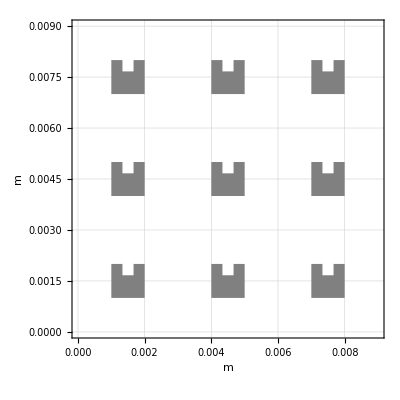

```mathematica
Show[background,
s = 0.001; (*scale*)
block = {Gray,Polygon[{{0,0},s{0,1},s{1/3,1},s{1/3,2/3},s{2/3,2/3},s{2/3,1},s{1,1},s{1,0}} ]};
Graphics[Table[Translate[{block},0.001{1+3x,1+3y}],{x,0,2},{y,0,2}]]]
```

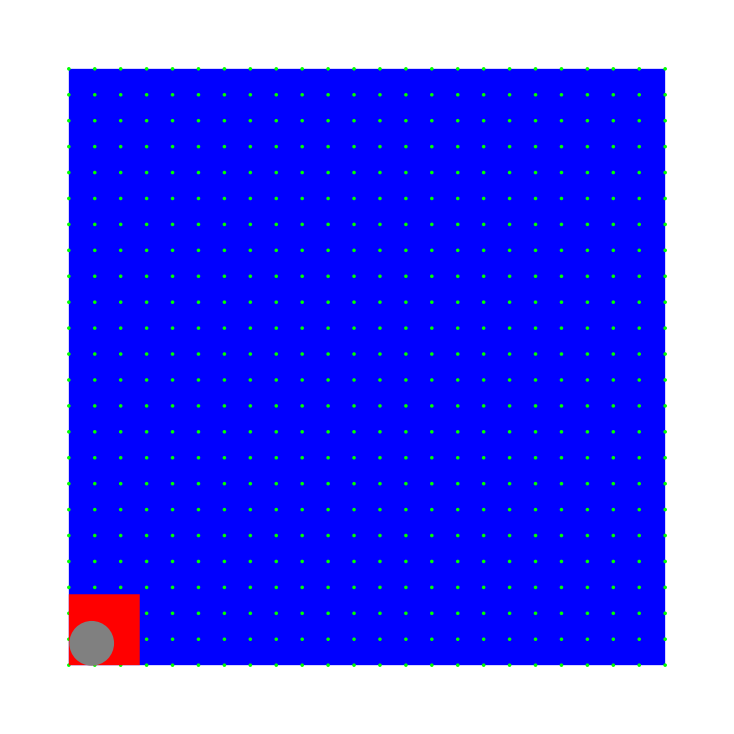

```mathematica
Graphics[{
(*voxel*)
Blue, Rectangle[{0,0},voxel7T{1,1}],
Green,
discsPerRow = perVoxelperRow⟦2⟧;
Table[Disk[{x,y}*(*2discRadii⟦3⟧*)voxel7T/discsPerRow,discRadii⟦2⟧],{x,0,discsPerRow},{y,0,discsPerRow}],


(*equivalent area of metal needed for 7T MRI*)
Red,Rectangle[minEdgeLength7T{0,0},minEdgeLength7T{1,1}],
(*15 micron Sphere*)
Gray,Disk[minimumVisibleSphereRad{1,1},minimumVisibleSphereRad]
}]
```

The most conservative measurements I have are for a 1.5 T MRI with a 0.2*10^-6 thick layer of Chrome steel, is a square with each side
0.12mm, 120 microns on a side.  1.52681×10^-8 square meters (0.015 mm^2).



Chrome steel reaches its magnetic saturation at 1.5 T.  The magnetic saturation of Chrome steel is 1.36 10^6 A/m; We can get proportional size decreases by choosing materials with higher magnetic saturations.

```mathematica
1.5268140296446394*^-8*10^6
```

0.0152681

```mathematica
NumberForm[0.015268140296446395,5]
```

0.015268

```mathematica
(*change in resolution from pixel edges of size (.5/.2)^3*)
(0.5/0.2)^3
```

15.625

```mathematica
SurfaceAreaThinFilmIn7T=1.5268140296446394*^-8/15.625*10^6 (* mm^2*)
SquareEdgeLength7T =Sqrt[SurfaceAreaThinFilmIn7T]
SurfaceAreaThinFilmIn7T*10^6
```

0.000977161

0.0312596

977.161

```mathematica
Sqrt[0.002442902447431423]
```

0.0494257

```mathematica
19.2^2
```

368.64

```mathematica
.13^2
```

0.0169

Paul, Using the imaging techniques I usually use, the net area of these thin devices is still somewhat large.The most conservative measurements I have are for a 1.5 T MRI, in which an 15-micron diameter chrome steel ball can be detected. Using 0.2*10^-6 thick layer of chrome steel, the net required area is a square with each side
0.093 mm (93 microns on a side), or 8.8^-9 square meters (0.009 mm^2).
We will be using animal MRIs, with smaller bores, higher magnetic fields, and corresponding better resolution. A 1.5 T MRI can image voxels 0.5 x0 .5 x0 .5 mm, while a 7 T MRI can image 0.2 x0 .2 x0 .2 mm.In a 7 T MRI, we can make these thin particles squares, 31 microns on a side.The area can be divided into many smaller particles because superposition holds for magnetism.We just need to ensure that there is a net area equal to 31 x31 microns inside a 0.2 x0 .2 x0 .2 mm voxel.These calculations were made using chrome steel, which reaches its magnetic saturation in even a 1.5 T MRI.The magnetic saturation of chrome steel is 1.36 10^6 A/m.We can get proportional size decreases by choosing materials with higher magnetic saturations.To use smaller particles/smaller densities probably requires custom coils.